# Inlämningsuppgift/Projektuppgift IX1303 Algebra och Geometri, VT2019, period4

Fredrik Öberg, TIDAB, fobe@kth.se

## Uppgift 1

Visa i ℝ^3 lösningsmängden till z ≥√(x^2+y^2)

```mathematica
Clear[x,y,z]
a=z>=√(x^2+y^2);
RegionPlot3D[a,{x,-100,100},{y,-100,100},{z,-100,100},AxesLabel->{x,y,z}]
```

-Graphics3D-

Med användandet av funktionen RegionPlot3D syns det att lösningsmängden till olikheten z ≥√(x^2+y^2) skapar ett underrum till R^3 som har formen av en kon med spetsen på Origo.

## Uppgift 2

Visa i ℝ^3 lösningsmängden till systemet 

	x^2 + y^2 + z^4 = 4
	x^2 + z^2 = 1

```mathematica
Clear[x,y,z]
W=x^2+y^2+z^2-4;
Q=x^2+y^2-1;
ContourPlot3D[{W==0},{x,-5,5},{y,-5,5},{z,-5,5},AxesLabel->{x,y,z}]
```

-Graphics3D-

Först ville jag visualisera hur lösningsmängden till ekvationen x^2 + y^2 + z^4 = 4 såg ut, och med det kan vi se att det lösningsmängden formar en sfär i R^3 med radie två längdenheter.

```mathematica
ContourPlot3D[{Q==0},{x,-5,5},{y,-5,5},{z,-5,5},AxesLabel->{x,y,z}]
```

-Graphics3D-

Därefter kan vi se att ekvationen x^2 + z^2 = 1 formar en cylinder i R^3 med radien 1 längdenheter och som är centrerad kring x = 0 och y = 0. Cylinderns mantelyta utgör lösningsmängden till den givna ekvationen.

```mathematica
ContourPlot3D[{W==0,Q==0},{x,-5,5},{y,-5,5},{z,-5,5},MeshFunctions->{Function[{x,y,z,f},W-Q]},MeshStyle->{{Blue, Thick}},Mesh->{{0}},ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,30]]]
```

-Graphics3D-

För att visa lösningsmängden till det givna ekvationssystemet så visualiseras båda ekvationerna samtidigt. Lösningsmängden till systemet är de två blåa cirklarna som visar skärningspunkterna mellan de båda givna ekvationerna.

## Uppgift 3

Lös grafiskt additionen av de tre vektorena:
	
		𝕒 = 3x + 2y
		𝕓 = -2x+y
		𝕔 = x - 3y

```mathematica
a ={3,2};
b ={-2,1};
c ={1,-3};
d = a+b
e = d+c
```

{1,3}

{2,0}

Först här ovan är en uträkning för att se vilka värden additionen av de givna vektorerna ger. Det säger oss att a + b ska hamna på punkten (1,3) och att a + b + c ska hamna på punkten (2,0).

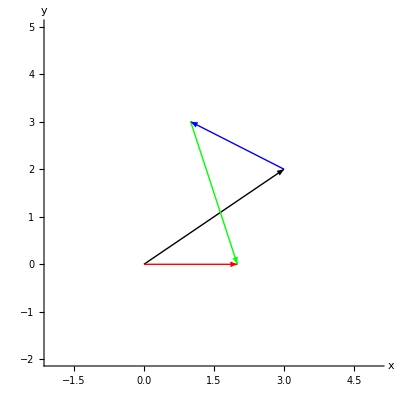

```mathematica
Graphics[{Thick,Black,Arrow[{{0,0},{3,2}}],Blue, Arrow[{{3,2},{1,3}}],Green,Arrow[{{1,3},{2,0}}],,Red,Arrow[{{0,0},{2,0}}]},Axes->True, PlotRange->{{-2,5},{-2,5}},AxesLabel->{x,y}]
```

Med den här visualiseringen där a är den svarta vektorn; b är den blå vektorn; c är den gröna vektorn samt att a + b + c är den  röda vektorn så kan vi se att visualiseringen av a + b + c stämmer överens med beräkningarna gjorda ovan.

## Uppgift 4

Lös grafiskt ekvationssystemet

x + 2y + 3z = 1
2x + 4y + 7z = 2
3x + 7y + 11z = 8

dvs plotta planen i ℝ^3 och se om det finns någon lösning.

```mathematica
A ={{1,2,3},{2,4,7},{3,7,11}};
b = {1,2,8};

LinearSolve[A,b]
```

{-9,5,0}

```mathematica
{-9,5,0}
```

{-9,5,0}

Först här ovan är en uträckning som algebraiskt ska visa lösningen för det givna ekvationssystemet. Den uträkningen visar att de givna planen ska mötas i punkten (-9,5,0).

```mathematica
a1=ContourPlot3D[x+2y+3z==1,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{x,y,z},Mesh->None,ContourStyle->Directive[Red]];
a2 =ContourPlot3D[2x+4y+7z==2,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{x,y,z},Mesh->None,ContourStyle->Directive[Blue]];
a3 =ContourPlot3D[3x+7y+11z==8,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{x,y,z},Mesh->None,ContourStyle->Directive[Green]];
```

```mathematica
Show[a1,a2,a3]
```

-Graphics3D-

För en grafisk lösning på ekvationssystemet så plottade jag varje plan var för sig genom funktionen “CountourPlot3D” och där gavs planen var sin färg. Det gav mig möjlighet att visualisera planen genom funktionen “Show” och där visas det tydligt att den tidigare beräkningen stämmer överens med visualiseringen. Planen möts i punkten (-9,5,0).

## Uppgift 7

Lös grafiskt ekvationssystemet

x − 2y = 3
3x + 5y = 17 , 

dvs plotta linjerna i ℝ^2 och se om det finns någon lösning.

```mathematica
Clear[x,y]
Solve[x-2y==3&&3x+5y==17,{x,y}]
```

{{x→49/11,y→8/11}}

Först löste jag ekvationssystemet algebraiskt för att se vid vilken punkt linjerna möts i. Detta gav värdena (49/11, 8/11).

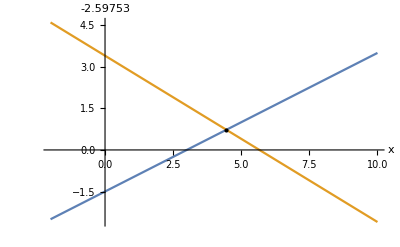

```mathematica
Plot[{y=(3-x)/(-2),y=(17-3x)/5},{x,-2,10},Epilog->{Black,PointSize@Large,Point[{49/11,8/11}]},AxesLabel->{x,y}]
```

I den grafiska lösningen ovan ser vi att linjerna skär varandra vid en viss punkt. För att bekräfta att det är samma punkt jag fick fram vid den algebraiska uträkningen så lades en svart punkt till på grafen med de givna värdena. Detta validerade de båda resultaten.

## Uppgift 8

Visa grafiskt varför följande system saknar lösning. 

	3x + 4y − z = 8
	6x + 8y − 2z = 3

```mathematica
a=ContourPlot3D[3x+4y-z==8,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{x,y,z},Mesh->None,ContourStyle->Directive[Black]];
b=ContourPlot3D[6x+8y-2z==3,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{x,y,z},Mesh->None,ContourStyle->Directive[Yellow]];

Show[a,b]
```

-Graphics3D-

Riktningsvektorerna på de givna planen <3,4-1> och <6,8,-2> indikerar att vi har att göra med parallella plan av den anledningen att de båda vektorerna är skalärer till varandra. Vid plottandet bekräftas denna indikation genom att det tydligt visualiseras att de båda planen verkligen är parallella. Det betyder att planen aldrig skär varandra, och därför har ekvationssystemet ingen lösning.

## Uppgift 9

Givet matriserna A, B och C. Beräkna i Mathematica matriserna A + B − C, ABC och CBA.

```mathematica
a1={{3,2,4},{7,8,0},{2,5,2}};
b1={{5,8,7},{6,4,9},{10,1,0}};
c1= {{5,1,5},{5,9,7},{6,8,2}};

MatrixForm[a1] MatrixForm[b1]MatrixForm[c1]
```

(3 | 2 | 4
7 | 8 | 0
2 | 5 | 2) (5 | 1 | 5
5 | 9 | 7
6 | 8 | 2) (5 | 8 | 7
6 | 4 | 9
10 | 1 | 0)

```mathematica
MatrixForm[a1+b1-c1]MatrixForm[a1.b1.c1]MatrixForm[c1.b1.a1]
```

(3 | 9 | 6
8 | 3 | 2
6 | -2 | 0) (674 | 774 | 412
1260 | 1542 | 828
1096 | 1422 | 620) (749 | 703 | 665
1581 | 1843 | 1273
844 | 874 | 684)

Den här uppgiften är ganska rakt på sak. Det intressanta är att se att det spelar roll för resultatet i vilken ordning matriser multpliceras.

## Uppgift 10

Beräkna Ax.

```mathematica
A={{1,7,8,9},{1,2,9,1},{1,5,1,5},{1,6,4,8}};
x={1,9,5,6};

MatrixForm[A]   
MatrixForm[x]
```

(1 | 7 | 8 | 9
1 | 2 | 9 | 1
1 | 5 | 1 | 5
1 | 6 | 4 | 8)

(1
9
5
6)

```mathematica
MatrixForm[A.x]
```

(158
70
81
123)

En ganska självklar uppgift men som ändå ger en insikt i hur linjära transformationer kan hanteras i Mathematica.

## Uppgift 15

Hitta egenvärdena till matrisen A.

```mathematica
A={{9,-4,-2,-4},{-56,32,-28,44},{-14,-14,6,-14},{42,-33,21,-45}};

MatrixForm[A]
```

(9 | -4 | -2 | -4
-56 | 32 | -28 | 44
-14 | -14 | 6 | -14
42 | -33 | 21 | -45)

```mathematica
Eigenvalues[A]
```

{13,13,-12,-12}

Genom funktionen Eigenvalues så fås det fram att matrisen A har egenvärdena 13 och -12, där båda egenvärdena har en multiplicitet av två.

## Uppgift 17

Hitta den radreducerade trappstegsmatrisen (rref) till matrisen A. Har matrisen någon redundans?

```mathematica
A={{2,4,8},{4,5,1},{7,9,3}};

MatrixForm[A]
```

(2 | 4 | 8
4 | 5 | 1
7 | 9 | 3)

```mathematica
MatrixForm[RowReduce[A]]
```

(1 | 0 | -6
0 | 1 | 5
0 | 0 | 0)

Med funktionen RowReduce ser vi att den sista raden i den radreducerade trappstegsmatrisen består av enbart nollor. Eftersom att vi har två pivå element(ettorna i kolumn ett och två) samt tre rader i matrisen, leder detta till att vi har en så kallad “fri variabel” i matrisen. Detta visar att matrisen är av den linjärt beroende typen vilket betyder att, i det här fallet, en av vektorerna (kolumnerna) i matrisen kan skapas som en skalär kombination av de andra två vektorerna. Då kan det fastställas att matrisen har redundans - en vektor som upprepar redan etablerad information i matrisen utan att tillföra någon ny.

## Uppgift 19

Visa att kolumnerna i matris A är ortogonala.

```mathematica
A={{-6,-3,6,1},{-1,2,1,-6},{3,6,3,-2},{6,-3,6,-1},{2,-1,2,3},{-3,6,3,2},{-2,-1,2,-3},{1,2,1,6}};
MatrixForm[A]
```

(-6 | -3 | 6 | 1
-1 | 2 | 1 | -6
3 | 6 | 3 | -2
6 | -3 | 6 | -1
2 | -1 | 2 | 3
-3 | 6 | 3 | 2
-2 | -1 | 2 | -3
1 | 2 | 1 | 6)

Av matrisens kolumner kan vi skapa fyra vektorer

```mathematica
v1 ={-6,-1,3,6,2,-3,-2,1};
v2={-3,2,6,-3,-1,6,-1,2};
v3={6,1,3,6,2,3,2,1};
v4={1,-6,-2,-1,3,2,-3,6};
```

Definitionen av ortognoalitet är när två vektorers inre produkt är lika med noll. Vi undersöker om så är fallet genom att låta vektorerna genomgå operationen skalärprodukt(“dot product” på engelska).

```mathematica
v1.v2
v1.v3
v1.v4
v2.v3
v2.v4
v3.v4
```

0

0

0

«3 more identical outputs»

Eftersom alla möjliga kombinationer av skalärprodukt(skalärprodukter har den kommutativa egenskapen att u.v = v.u) har den inre produkten noll, så kan vi säkerställa att kolumnerna i matrisen A är ortogonala,

## Uppgift 20

Ange diagonalmatrisen D och matriserna P och P^-1 som används för diagonalisering av A.

```mathematica
Clear[A,D1,P,P1]

A={{-6,4,0,9},{-3,0,1,6},{-1,-2,1,0},{-4,4,0,7}};

MatrixForm[A]
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

```mathematica
Eigenvalues[A]
```

{5,-2,-2,1}

```mathematica
D1={{5,0,0,0},{0,-2,0,0},{0,0,-2,0},{0,0,0,1}};

MatrixForm[D1]
```

(5 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | 1)

Diagonalmatrisen D fås av att sätta matrisen A's eigenvärden - vilka vi fått fram genom funktionen Eigenvalues - på diagonalen i en nxn matris. Denna matris ser vi ovan genom variabeln D1.

```mathematica
P=Transpose[Eigenvectors[A]];

MatrixForm[P]
```

(2 | 6 | 1 | 2
1 | -3 | 1 | -1
-1 | 0 | 1 | -7
2 | 4 | 0 | 2)

Matrisen P består av kolumnen A's egenvektorer och dessa egenvektorer fås i mathematica fram genom att använda funktionen Eigenvectors. Av någon anledning gavs egenvektorerna ut som radvektorer i stället för kolumnvektorer av den använda funktionen. Detta gav felaktiga värden inledningsvis när jag undersökte värdena längre ner i uppgiften. Det är av den anledningen variebeln P tilldelas värdena av transponatet(Transpose) på matrisen som gavs av funktionen Eigenvectors.

```mathematica
P1=Inverse[P];

MatrixForm[P1]
```

(-5/14 | 2/7 | 1/14 | 3/4
2/21 | -1/7 | 1/21 | 0
17/21 | 2/7 | -2/21 | -1
1/6 | 0 | -1/6 | -1/4)

P^-1 är P - matrisens invers och fås i mathematica fram genom funktionen Inverse och resultatet kan ses ovan genom variabeln P1.

```mathematica
Q=P.D1.P1;
MatrixForm[Q]
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

För att bekräfta att vi fått fram rätt värden hos de olika matriserna(P, D1 och P1) så avslutar vi uppgiften med multiplikationen PDP^-1. Där kan vi se ovan genom variabeln Q att vi får fram matrisen A. Det är den matrisen vi ska få fram genom operationen, vilket bekräftar att värdena i matriserna P,P1 och D1 är korrekta.